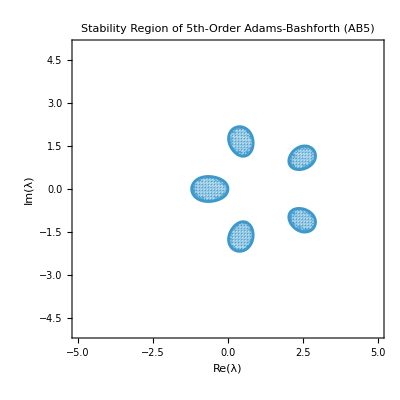

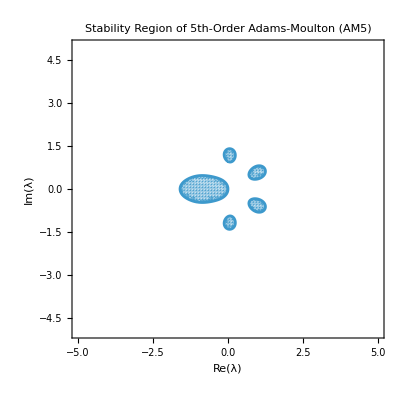

```mathematica
(*Define the stability polynomial for the 5th-order Adams-Bashforth method*)
RAB5[λ_]:=1+(190 λ-277 λ^2+261 λ^3-127 λ^4+25 λ^5)/720;
(*Define the stability polynomial for the 5th-order Adams-Moulton method*)
RAM5[λ_]:=1+(190 λ-277 λ^2+261 λ^3-127 λ^4+25 λ^5)/720+(190 λ^6)/720;

(*Define the condition for stability (the modulus should be<=1)*)
stabilityConditionAB5[λ_]:=Abs[RAB5[λ]]<=1;
stabilityConditionAM5[λ_]:=Abs[RAM5[λ]]<=1;

(*Create a mesh of complex numbers (λ) in the complex plane*)
ReMin=-5;ReMax=5;
ImMin=-5;ImMax=5;

(*Plot the stability region for Adams-Bashforth AB5*)
RegionPlot[stabilityConditionAB5[x+I y],{x,ReMin,ReMax},{y,ImMin,ImMax},
PlotPoints->100,AspectRatio->1,FrameLabel->{"Re(λ)","Im(λ)"},
PlotLabel->"Stability Region of 5th-Order Adams-Bashforth (AB5)",Axes->True]

(*Create a mesh of complex numbers (λ) in the complex plane*)
RegionPlot[stabilityConditionAM5[x+I y],{x,ReMin,ReMax},{y,ImMin,ImMax},
PlotPoints->100,AspectRatio->1,FrameLabel->{"Re(λ)","Im(λ)"},
PlotLabel->"Stability Region of 5th-Order Adams-Moulton (AM5)",Axes->True]
```